Note: In this problem set, there are no green cells, because no answers match the text answers.

```mathematica
Clear["Global`*"]
```

2 - 9 Verifications. Derivations. Comparisons.

9.  Natural spline condition. Using the given coefficients, verify that the spline in example 2 satisfies g''[x] = 0 at the ends.

```mathematica
Clear["Global`*"]
```

The top part of this section does not really apply to the problem. The points are from the example referred to by the problem.

```mathematica
data={{0,3.9},{-0.8,3.5},{-1.5,2.7},{-2.5,2.2},{-4.0,1.8},{-5.,1.5},{-5.8,0}}
```

{{0,3.9},{-0.8,3.5},{-1.5,2.7},{-2.5,2.2},{-4.,1.8},{-5.,1.5},{-5.8,0}}

Some examples of use of interpolating polynomials was done in the last section. I’m keeping this in here for now, because it shows up in the plot.

```mathematica
inpp[x_]=InterpolatingPolynomial[data,x]
```

(5.8+x) (0.672414+x (0.00229885+(2.5+x) (0.0561303+(4.+x) (-0.024302+(0.8+x) (0.00397479-0.00635968 (5.+x))))))

```mathematica
Simplify[%]
```

3.9-1.2009 x-3.66164 x^2-2.4553 x^3-0.754728 x^4-0.111135 x^5-0.00635968 x^6

I take a derivative out of curiosity, but it doesn’t relate to the direction the problem should be going.

```mathematica
dinpp=Simplify[D[inpp[x],{x,2}]]
```

-7.32327-14.7318 x-9.05673 x^2-2.22271 x^3-0.190791 x^4

With the two cells below, I find that the interpolated spline I came up with is clamped at the ends.

```mathematica
dinpp/.x->0
```

-7.32327

```mathematica
dinpp/.x->6
```

-1149.13

Next is the polynomial which the text says accompanies the figure on example 2, p. 825.

```mathematica
tex[x_]=3.900-0.65083 x^2+0.033858 x^4+0.011041 x^6-0.0014010 x^8+0.000055595 x^10-0.00000071867 x^12
```

3.9-0.65083 x^2+0.033858 x^4+0.011041 x^6-0.001401 x^8+0.000055595 x^10-7.1867×10^-7 x^12

Also without much purpose, I take a derivative of this function.

```mathematica
dtex=Simplify[D[tex[x],{x,2}]]
```

-1.30166+0.406296 x^2+0.33123 x^4-0.078456 x^6+0.00500355 x^8-0.0000948644 x^10

```mathematica
dtex/.x->0
```

-1.30166

```mathematica
dtex/.x->6
```

-549.891

Now I plot the two polynomials, but neither is g[x], or really relates to what was asked.

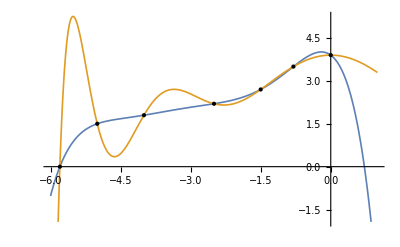

```mathematica
Plot[{inpp[x],tex[x]},{x,-6,1},PlotStyle->Thickness[0.003],Epilog->Map[Point,data]]
```

A formula from the text, meant to calculate q_0 is apparently not right

```mathematica
Subscript[q, 0][x_]=3.9+0(x+5.8)-0.61(x+5.8)^2-0.015(x+5.8)^3
```

3.9-0.61 (5.8+x)^2-0.015 (5.8+x)^3

or I am applying it wrong

```mathematica
Solve[Subscript[q, 0]''[x]==0,x]
```

{{x→-19.3556}}

which is demonstrated by the next two cells not equaling zero.

```mathematica
Subscript[q, 0]''[.8]
```

-1.814

```mathematica
Subscript[q, 0]''[0]
```

-1.742

Now switching to the text answer to ponder it. First, in working it out, I see that the below cell produces the value the text refers to as its near-zero. The -1.39 and 0.58 coefficients show that the text is looking at the last two columns of the final row of the table at the bottom of p. 825. But why are there no terms for a_j0 and a_j1? As in the calculation of g[x] in example 1 on p. 824, it appears that something made the zeroth and first terms drop out, even though values for a_j0 and a_j1 are shown in the table on p. 825. Maybe some day I will come back to it and try again to figure out how that happened.

```mathematica
Subscript[q, 5][x_]=-1.39(x-5)^2+0.58(x-5)^3
```

-1.39 (-5+x)^2+0.58 (-5+x)^3

```mathematica
Subscript[q, 5]''[5.8]
```

0.004

10 - 16 Determination of splines.
Find the cubic spline g[x] for the given data with k_0 and k_n as given.

11.  If we started from the piecewise linear function in figure 438, we would obtain g[x] in problem 10 as the spline satisfying g'[-2] = f'[-2] = 0, g'[2] = f'[2] = 0. Find and sketch or graph the corresponding interpolation polynomial of 4th degree and compare it with the spline. Comment.

```mathematica
kru=RGBColor[0.392,0.823,0.98];
innerbw=RGBColor[.97,.97,.994];
pts={{-2,0},{-0.4,-0.5},{-0.9,0.85},{0,1}};
ptsR={{2,0},{0.4,-0.5},{0.9,0.85},{0,1}};
ptsL={{-2,0},{-1.1,-1.5},{-1,1},{0,1}};
ptsR2={{2,0},{1.1,-1.5},{1,1},{0,1}};
```

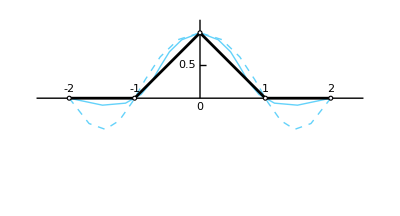

```mathematica
g1=Graphics[{{kru,BezierCurve[pts],Opacity[0.0],Green,Line[pts],Red,Point[pts]},{kru,Dashed,BezierCurve[ptsL],Opacity[0.0],Green,Line[ptsL],Red,Point[ptsL]},{kru,BezierCurve[ptsR],Opacity[0.0],Green,Line[ptsR],Red,Point[ptsR]},{kru,Dashed,BezierCurve[ptsR2],Opacity[0.0],Green,Line[ptsR2],Red,Point[ptsR2]},{Line[{{0,0},{0,1.2}}]},{Line[{{0,0.5},{0.1,.5}}]},{Line[{{-2.5,0},{2.5,0}}]},{Thickness[0.005],Line[{{-2,0},{-1,0},{0,1},{1,0},{2,0}}]},{EdgeForm[Directive[Black]],innerbw,Disk[{-2,0},0.03]},{EdgeForm[Directive[Black]],innerbw,Disk[{-1,0},0.03]},{EdgeForm[Directive[Black]],innerbw,Disk[{0,1},0.03]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,0},0.03]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,0},0.03]},{Text[Style["-2",Medium],{-2,0.14}]},{Text[Style["2",Medium],{2,0.14}]},{Text[Style["-1",Medium],{-1,0.14}]},{Text[Style["1",Medium],{1,0.14}]},{Text[Style["0",Medium],{0,-0.14}]},{Text[Style["0.5",Medium],{-0.2,0.5}]}},ImageSize->400]
```

```mathematica
Clear["Global`*"]
```

```mathematica
data={{-2,0},{-1,0},{0,1},{1,0},{2,0}}
```

{{-2,0},{-1,0},{0,1},{1,0},{2,0}}

```mathematica
inpp[x_]=InterpolatingPolynomial[data,x]
```

(1+x) (2+x) (1/2+(-1/2+1/4 (-1+x)) x)

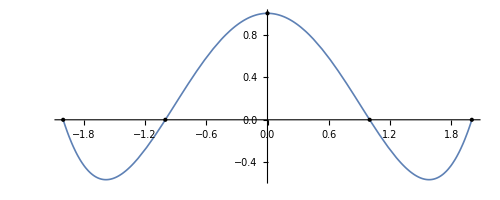

```mathematica
p1=Plot[{inpp[x]},{x,-2,2},PlotStyle->Thickness[0.003],AspectRatio->Automatic,Epilog->Map[Point,data]]
```

The plot above happens to be of 4th degree, as requested. It looks a lot like the dashed curve above. Using the method of piecewise poly described in problem 13 and 15, I could get something pretty close to the solid curve in the multi-curve plot, I think.

13. f_0 = f[0] = 1,  f_1 = f[1] =0,  f_2 = f[2] =-1
f_3 = f[3] = 0, k_0 = 0, k_3 = -6

```mathematica
Clear["Global`*"]
```

```mathematica
Needs["Splines`"]
```

Bounced around for awhile looking for an easy way to work with splines. The text wants to give only control points, plus the first derivatives at the ends. This is enough descriptive info to plot a solution, but within Mathematica documentation, and considering most of what I found on-line, the talk was about basis splines, knots, and weights as well as control points. I finally found an excellent resource in Ray Koopman’s answer to SEMma question https://mathematica.stackexchange.com/questions/35405/extracting-polynomials-from-a-cubic-spline-function. It goes straight for the piecewise poly equation without messing around with that other spline stuff. I like splines, but as J.M. says in the question site just referenced, “Unfortunately, as it stands, BSplineFunction[] objects are immune to exposure from PiecewiseExpand[].”

A comment about the first section. It seems that Solve cannot handle more than three control points at a time. I commented out some second derivative conditions that I don’t think are necessary, in order to make room for some crucial first derivative conditions, without overloading Solve. I had to play with it a little, because the join at x=2, though smooth, was lopsided at first. With yellow below,  I simply picked out a first derivative that I thought would look good, and then matched it with the calculation of f3.

```mathematica
dat={{0,1},{1,0},{2,-1},{3,0}};
```

```mathematica
f1[x_]=a1+b1*x+c1*x^2+d1*x^3;
f2[x_]=a2+b2*x+c2*x^2+d2*x^3;
s=Solve[{f1@dat[[1,1]]==dat[[1,2]],f1@dat[[2,1]]==dat[[2,2]],f2@dat[[2,1]]==dat[[2,2]],f2@dat[[3,1]]==dat[[3,2]],f1'@dat[[2,1]]==f2'@dat[[2,1]],(*f1''@dat[[2,1]]==f2''@dat[[2,1]],*)f1''@dat[[1,1]]==0,(*f2''@dat[[3,1]]==0,*)f1'@dat[[1,1]]==0,f2'@dat[[3,1]]==1.5},{a1,b1,c1,d1,a2,b2,c2,d2}]
```

{{a1→1.,b1→0.,c1→0.,d1→-1.,a2→4.,b2→-4.5,c2→5.32907×10^-15,d2→0.5}}

After taking care of the first two pieces, I have to do the last one. With pink, I requested a smooth join at x=2. I found out I could not get that join smooth and have the second derivative equal zero on the right end. So I guess that means the right end is “clamped”, and not “free” or “natural” in the terms of the text, p. 823. However, I do not see that it violates the problem description to have it clamped.

```mathematica
f1[x_]=a1+b1*x+c1*x^2+d1*x^3/.{a1->1,b1->0,c1->0,d1->-1}
f2[x_]=a2+b2*x+c2*x^2+d2*x^3/.{a2->4,b2->-4.5,c2->0,d2->0.5}
f3[x_]=a3+b3*x+c3*x^2+d3*x^3;

s2=N[Solve[{f3@dat[[3,1]]==dat[[3,2]],f3@dat[[4,1]]==dat[[4,2]],f3'@dat[[3,1]]==1.5,f3'@dat[[4,1]]==-6(*,f3''@dat[[4,1]] == 0*)},{a3,b3,c3,d3}]]
```

```mathematica
1-x^3  (* text solution 1-x^2 *)
```

```mathematica
4-4.5 x+0.5 x^3  (* text solution -2(x-1)-(x-1)^2+2(x-1)^3 *)
```

{{a3→72.,b3→-100.5,c3→45.,d3→-6.5}}

```mathematica
f3[x_]=a3+b3*x+c3*x^2+d3*x^3/.{a3->72,b3->-100.5,c3->45,d3->-6.5}
```

```mathematica
72-100.5 x+45 x^2-6.5 x^3  (* text solution -1 +2(x-2)+5(x-2)^2-6(x-2)^3 *)
```

```mathematica
f[x_]=Piecewise[{{f1[x],0≤x≤1},{f2[x],1≤x≤2},{f3[x],2≤x≤3}}]
```

Piecewise[{{1-x^3, 0≤x≤1}, {4-4.5 x+0.5 x^3, 1≤x≤2}, {72-100.5 x+45 x^2-6.5 x^3, 2≤x≤3}, {0, True}}]

Incidentally, none of the poly pieces matches the equations listed in the text answer.

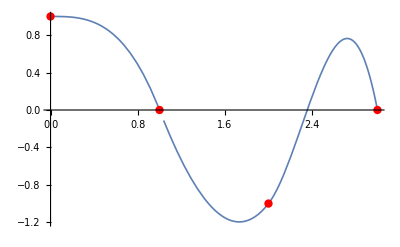

```mathematica
Plot[f[x],{x,0,3},PlotStyle->Thickness[0.003],Epilog->{Red,PointSize[0.015],Point/@dat}]
```

I feel fairly satisfied with this problem. It seems like a fairly general way to build piecewise cubic polys when they are needed.

15.  f_0 = f[0] = 4,  f_1 = f[2] =0,  f_2 = f[4] =-4
f_3 = f[6] = 78, k_0 = 0, k_3 = 0

```mathematica
Clear["Global`*"]
```

```mathematica
dat={{0,4},{2,0},{4,-4},{6,78}};
```

I didn’t ask for the Splines package here, and I didn’t need it. I was able to copy everything from the last problem, change the designation of control points, and do a minor tweak on the join at x=4, choosing a reasonable value of  the first derivative.

```mathematica
f1[x_]=a1+b1*x+c1*x^2+d1*x^3;
f2[x_]=a2+b2*x+c2*x^2+d2*x^3;
s=Solve[{f1@dat[[1,1]]==dat[[1,2]],f1@dat[[2,1]]==dat[[2,2]],f2@dat[[2,1]]==dat[[2,2]],f2@dat[[3,1]]==dat[[3,2]],f1'@dat[[2,1]]==f2'@dat[[2,1]],(*f1''@dat[[2,1]]==f2''@dat[[2,1]],*)f1''@dat[[1,1]]==0,(*f2''@dat[[3,1]]==0,*)f1'@dat[[1,1]]==0,f2'@dat[[3,1]]==1.0},{a1,b1,c1,d1,a2,b2,c2,d2}]
```

{{a1→4.,b1→0.,c1→0.,d1→-0.5,a2→24.,b2→-19.,c2→4.,d2→-0.25}}

```mathematica
f1[x_]=a1+b1*x+c1*x^2+d1*x^3/.{a1->4,b1->0,c1->0,d1->-1/2}
f2[x_]=a2+b2*x+c2*x^2+d2*x^3/.{a2->24.,b2->-19.,c2->4.,d2->-0.25}
f3[x_]=a3+b3*x+c3*x^2+d3*x^3;
```

```mathematica
4-x^3/2 (* text solution 4+x^2-x^3  *)
```

```mathematica
24.-19. x+4. x^2-0.25 x^3  (* text solution -8(x-2)-5(x-2)^2+5(x-2)^3 *)
```

```mathematica
s2=N[Solve[{f3@dat[[3,1]]==dat[[3,2]],f3@dat[[4,1]]==dat[[4,2]],f3'@dat[[3,1]]==1.0,f3'@dat[[4,1]]==0(*,f3''@dat[[4,1]] == 0*)},{a3,b3,c3,d3}]]
```

{{a3→2256.,b3→-1455.,c3→303.5,d3→-20.25}}

```mathematica
f3[x_]=a3+b3*x+c3*x^2+d3*x^3/.{a3->2256,b3->-1455,c3->303.5,d3->-20.25}
```

```mathematica
2256-1455 x+303.5 x^2-20.25 x^3  (* text solution 4+32(x-4)+25(x-4)^2-11(x-4)^3  *)
```

```mathematica
f[x_]=Piecewise[{{f1[x],0≤x≤2},{f2[x],2≤x≤4},{f3[x],4≤x≤6}}]
```

Piecewise[{{4-x^3/2, 0≤x≤2}, {24.-19. x+4. x^2-0.25 x^3, 2≤x≤4}, {2256-1455 x+303.5 x^2-20.25 x^3, 4≤x≤6}, {0, True}}]

```mathematica
p1=Plot[f[x],{x,0,6},PlotStyle->Thickness[0.003],PlotRange->{{-0.5,7},{-15,90}},ImageSize->300,Epilog->{Red,PointSize[0.015],Point/@dat}];
```

```mathematica
p2=Plot[f[x],{x,0,6},PlotStyle->Thickness[0.003],PlotRange->{{3,4.6},{-10,10}},ImageSize->300,Epilog->{Red,PointSize[0.015],Point/@dat}];
```

The plots below show that all is okay at x=4. However, none of the piecewise equations match the answer in the text. Again, I feel this approach could be useful.

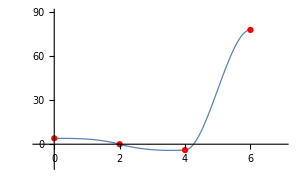
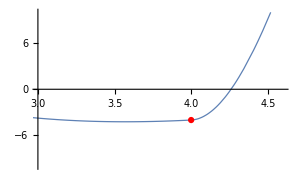

```mathematica
Row[{p1,p2}]
```

17.  If a cubic spline is three times continuously differentiable (that is, it has continuous first, second, and third derivatives), show that it must be a single polynomial.

Hmm, sounds slightly intriguing.